Klein-Nishina cross section

Notebook: Óscar Amaro, April 2023 @ GoLP-EPP

Introduction
In this notebook we present some calculations useful when using the KN unpolarized cross section https://en.wikipedia.org/wiki/Klein%E2%80%93Nishina_formula

```mathematica
(*d/dΩ=dσ/(sin θ dθ)->dσ/dθ=sin θ dσ/dΩ*)

Clear[re,λ,λp,λc,dσdΩ,dσdθ,dσdΩ0,ϵ,c,e,ϵeV,dσdΩlow,cdf,getθ]

λp=λ(1+ϵ(1-Cos[θ])); (*λp = λ', ϵ = λc/λ = Eγ/mc^2*)
dσdΩ=re^2/2(λ/λp)^2(λ/λp+λp/λ-Sin[θ]^2)//Simplify

(* low energy limit and total cross-section *)
dσdΩlow=Limit[dσdΩ,ϵ->0]//Simplify
2π Integrate[dσdΩlow Sin[θ],{θ,0,π}]//Simplify

(* normalized cumulative integral, aka, CDF *)
dσdΩcdf=2π Integrate[dσdΩ,θ]//Simplify
(* as expected, the CDF cannot be analytically inverted Solve[dσdΩCDF==v,θ]*)
```

(re^2 (1+ϵ-ϵ Cos[θ]+1/(1+ϵ-ϵ Cos[θ])-Sin[θ]^2))/(2 (1+ϵ-ϵ Cos[θ])^2)

1/4 re^2 (3+Cos[2 θ])

(8 π re^2)/3

(π re^2 (2 θ+(2 (-2-10 ϵ-12 ϵ^2+4 ϵ^3+11 ϵ^4) ArcTanh[√(-1-2 ϵ) Tan[θ/2]])/(-1-2 ϵ)^(5/2)+(ϵ^3 Sin[θ])/((1+2 ϵ) (1+ϵ-ϵ Cos[θ])^2)-(ϵ (2+8 ϵ+11 ϵ^2+3 ϵ^3) Sin[θ])/((1+2 ϵ)^2 (-1-ϵ+ϵ Cos[θ]))))/(2 ϵ^2)

```mathematica
dσdΩcdfπ=Limit[dσdΩcdf,θ->π,Direction->"FromBelow"]
```

(π^2 re^2 (-2-10 ϵ-12 ϵ^2+4 ϵ^3+11 ϵ^4+2 (1+2 ϵ)^(5/2)))/(2 ϵ^2 (1+2 ϵ)^(5/2))

```mathematica
Refine[(dσdΩ/Limit[dσdΩ,θ->0]/.{ϵeV->510998.95r})//Simplify,{θ>0,r>0}]
```

(1+ϵ-ϵ Cos[θ]+1/(1+ϵ-ϵ Cos[θ])-Sin[θ]^2)/(2 (1+ϵ-ϵ Cos[θ])^2)

```mathematica
Refine[(dσdΩcdf/dσdΩcdfπ/.{ϵeV->510998.95r})//Simplify,{θ>0,r>0}]//Simplify
```

((1+2 ϵ)^(5/2) (2 θ+(2 (-2-10 ϵ-12 ϵ^2+4 ϵ^3+11 ϵ^4) ArcTanh[√(-1-2 ϵ) Tan[θ/2]])/(-1-2 ϵ)^(5/2)+(ϵ^3 Sin[θ])/((1+2 ϵ) (1+ϵ-ϵ Cos[θ])^2)-(ϵ (2+8 ϵ+11 ϵ^2+3 ϵ^3) Sin[θ])/((1+2 ϵ)^2 (-1-ϵ+ϵ Cos[θ]))))/(π (-2-10 ϵ-12 ϵ^2+4 ϵ^3+11 ϵ^4+2 (1+2 ϵ)^(5/2)))

```mathematica
(* the number of harmonics of KN cross section in the ϵeV->0 limit is very small (Sin^2) and the Fourier transform is very simple. however, in the general case this is not true *)
(*FourierTransform[dσdΩ,θ,kθ]//Simplify*)
```

1.95634×10^-6 ϵeV

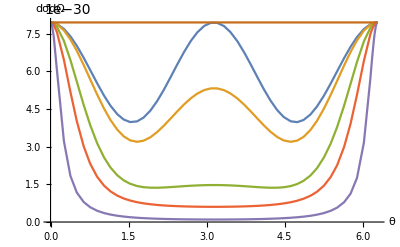

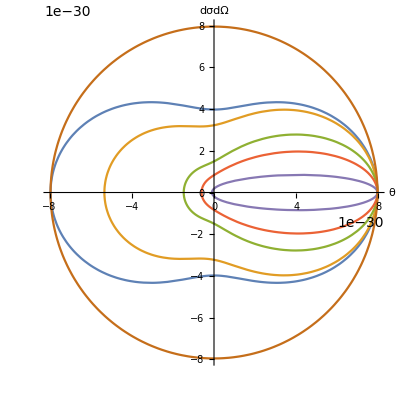

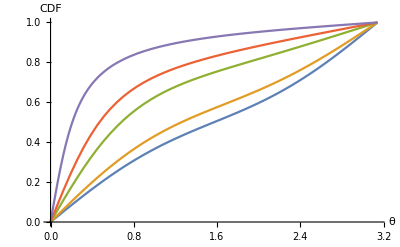

```mathematica
c=3 10^8;
e=1.6 10^-19;
ℏ=1.05 10^-34;
re=2.82 10^-15;
λc=2.42 10^-12;
ϵ=λc/λ;
λ=2π c/ω;
ω=e ϵeV/ℏ;
ϵ
(* λ =(2π c)/ω, ℏω/e=ϵeV*)
dσdΩ0=dσdΩ/.{θ->0};
Plot[{dσdΩ/.{ϵeV->2.75},dσdΩ/.{ϵeV->60 10^3},dσdΩ/.{ϵeV->511 10^3},dσdΩ/.{ϵeV->1.46 10^6},dσdΩ/.{ϵeV->10 10^6},dσdΩ0},{θ,0,2π},AxesLabel->{"θ","dσdΩ"}]

PolarPlot[{dσdΩ/.{ϵeV->2.75},dσdΩ/.{ϵeV->60 10^3},dσdΩ/.{ϵeV->511 10^3},dσdΩ/.{ϵeV->1.46 10^6},dσdΩ/.{ϵeV->10 10^6},dσdΩ0},{θ,0,2π},AxesLabel->{"θ","dσdΩ"}]

Plot[{dσdΩcdf/dσdΩcdfπ/.{ϵeV->2.75},dσdΩcdf/dσdΩcdfπ/.{ϵeV->60 10^3},dσdΩcdf/dσdΩcdfπ/.{ϵeV->511 10^3},dσdΩcdf/dσdΩcdfπ/.{ϵeV->1.46 10^6},dσdΩcdf/dσdΩcdfπ/.{ϵeV->10 10^6}},{θ,0,π},AxesLabel->{"θ","CDF"}]
```

(0.159155 (1+3.91269×10^-6 ϵeV)^(5/2) HeavisideTheta[π-θ] (2 θ+1/((-1-3.91269×10^-6 ϵeV)^(5/2))2 (-2-0.0000195634 ϵeV-4.59273×10^-11 ϵeV^2+2.99499×10^-17 ϵeV^3+1.61129×10^-22 ϵeV^4) ArcTanh[√(-1-3.91269×10^-6 ϵeV) Tan[θ/2]]+(7.48746×10^-18 ϵeV^3 Sin[θ])/((1+3.91269×10^-6 ϵeV) (1+1.95634×10^-6 ϵeV-1.95634×10^-6 ϵeV Cos[θ])^2)-(1.95634×10^-6 ϵeV (2+0.0000156507 ϵeV+4.21×10^-11 ϵeV^2+2.24624×10^-17 ϵeV^3) Sin[θ])/((1+3.91269×10^-6 ϵeV)^2 (-1-1.95634×10^-6 ϵeV+1.95634×10^-6 ϵeV Cos[θ]))))/(-2+2 (1+3.91269×10^-6 ϵeV)^(5/2)-0.0000195634 ϵeV-4.59273×10^-11 ϵeV^2+2.99499×10^-17 ϵeV^3+1.61129×10^-22 ϵeV^4)+HeavisideTheta[-π+θ] (1-(0.159155 (1+3.91269×10^-6 ϵeV)^(5/2) (2 (2 π-θ)+1/((-1-3.91269×10^-6 ϵeV)^(5/2))2 (-2-0.0000195634 ϵeV-4.59273×10^-11 ϵeV^2+2.99499×10^-17 ϵeV^3+1.61129×10^-22 ϵeV^4) ArcTanh[√(-1-3.91269×10^-6 ϵeV) Tan[1/2 (2 π-θ)]]-(7.48746×10^-18 ϵeV^3 Sin[θ])/((1+3.91269×10^-6 ϵeV) (1+1.95634×10^-6 ϵeV-1.95634×10^-6 ϵeV Cos[θ])^2)+(1.95634×10^-6 ϵeV (2+0.0000156507 ϵeV+4.21×10^-11 ϵeV^2+2.24624×10^-17 ϵeV^3) Sin[θ])/((1+3.91269×10^-6 ϵeV)^2 (-1-1.95634×10^-6 ϵeV+1.95634×10^-6 ϵeV Cos[θ]))))/(-2+2 (1+3.91269×10^-6 ϵeV)^(5/2)-0.0000195634 ϵeV-4.59273×10^-11 ϵeV^2+2.99499×10^-17 ϵeV^3+1.61129×10^-22 ϵeV^4))

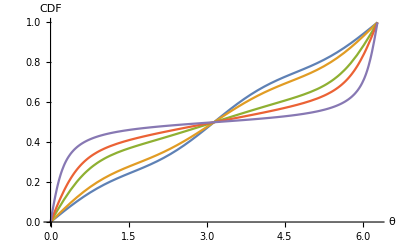

```mathematica
f=dσdΩcdf/(2dσdΩcdfπ)HeavisideTheta[π-θ]+HeavisideTheta[θ-π](1-dσdΩcdf/(2dσdΩcdfπ)/.{θ->2π-θ})
Plot[{f/.{ϵeV->2.75},f/.{ϵeV->60 10^3},f/.{ϵeV->511 10^3},f/.{ϵeV->1.46 10^6},f/.{ϵeV->10 10^6}},{θ,0,2π },AxesLabel->{"θ","CDF"}]
(*PolarPlot[{f/.{ϵeV->2.75},f/.{ϵeV->60 10^3},f/.{ϵeV->511 10^3},f/.{ϵeV->1.46 10^6},f/.{ϵeV->10 10^6}},{θ,0,2π },AxesLabel->{"θ","CDF"}]*)
```

```mathematica
cdf=dσdΩcdf/dσdΩcdfπ//Simplify;
getθ[r_,ϵeVr_]:=NSolve[{(cdf/.{ϵeV->ϵeVr})-r==0,0<=θ<=π},θ,Reals][[1,1,2]]
getθ[0.001,10 10^6]
```

0.000333345

```mathematica
Nsmpl=300;
rdist=RandomReal[{0,1},{Nsmpl}];
θdist=ParallelTable[getθ[rdist[[i]],10 10^6],{i,1,Length[rdist]}];
```

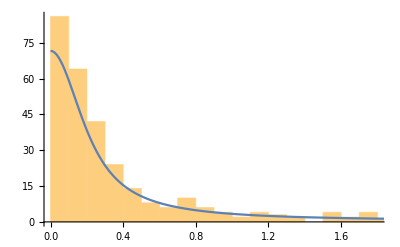

```mathematica
Show[{Histogram[θdist,40],Plot[{9 10^30 dσdΩ/.{ϵeV->10 10^6}},{θ,0,π},AxesLabel->{"θ","dσdΩ"},PlotRange->All]}]
```